# Omicron US analysis: Plotting partitioned case counts and Rt

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-us

```mathematica
dataset="omicron-us";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=250;
```

```mathematica
statesToDrop={"Washington"};
```

```mathematica
gridCount=4;
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron"};
```

```mathematica
n=Length[variants]
```

3

```mathematica
legendPanel=PointLegend[colors,variants,LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

PointLegend[colors,{other,Delta,Omicron},LegendMarkerSize→20,LegendLayout→{Row,1},Spacings→{0,1}]

### Colors

```mathematica
colors=Prepend[Table[ColorData["Rainbow"][i],{i,{0.3,0.95}}],Gray]
```

{GrayLevel[0.5],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004]}

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-11-01","2021-12-01","2022-01-01","2022-02-01","2022-03-01","2022-04-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

## Rt estimates

Using GARW (growth autoregressive random walk) model

```mathematica
rtData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_Rt-combined-"<>model<>".tsv"];
```

```mathematica
header=rtData[[1]]
```

{date,location,variant,median_R,median_freq,R_upper_95,R_lower_95,R_upper_80,R_lower_80,R_upper_50,R_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_R→4,median_freq→5,R_upper_95→6,R_lower_95→7,R_upper_80→8,R_lower_80→9,R_upper_50→10,R_lower_50→11}

```mathematica
rtData=Drop[rtData,1];
```

```mathematica
startDate=First[Sort[rtData[[All,1]]]]
```

2021-10-15

```mathematica
startDate="2021-11-01";
```

```mathematica
modelEndDate=Last[Sort[rtData[[All,1]]]]
```

2022-02-17

```mathematica
endDate=Last[Sort[rtData[[All,1]]]]
```

2022-02-17

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
states=Union[rtData[[All,2]]]
```

{Alabama,Arizona,Arkansas,California,Colorado,Connecticut,Delaware,Florida,Georgia,Hawaii,Illinois,Indiana,Kentucky,Louisiana,Maryland,Massachusetts,Michigan,Minnesota,Nebraska,Nevada,New Hampshire,New Jersey,New Mexico,New York,North Carolina,North Dakota,Ohio,Oklahoma,Oregon,Pennsylvania,South Carolina,Tennessee,Texas,Utah,Vermont,Virginia,Washington,Wisconsin}

```mathematica
states=DeleteCases[states,x_/;MemberQ[statesToDrop,x]]
```

{Alabama,Arizona,Arkansas,California,Colorado,Connecticut,Delaware,Florida,Georgia,Hawaii,Illinois,Indiana,Kentucky,Louisiana,Maryland,Massachusetts,Michigan,Minnesota,Nebraska,Nevada,New Hampshire,New Jersey,New Mexico,New York,North Carolina,North Dakota,Ohio,Oklahoma,Oregon,Pennsylvania,South Carolina,Tennessee,Texas,Utah,Vermont,Virginia,Wisconsin}

```mathematica
Length[states]
```

37

Only keep Rt data points when the variant is frequent enough to have a good estimate

```mathematica
rtData=Cases[rtData,x_/;x[[5]]>0.001];
```

```mathematica
rtData=DeleteCases[rtData,x_/;x[[2]]=="South Africa"&&x[[5]]<0.01];
```

```mathematica
rtGather[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
rtGatherLower[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,9}]]
```

```mathematica
rtGatherUpper[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
variantCountryRtPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=rtGather[country,variant];
lowerSeries=rtGatherLower[country,variant];
upperSeries=rtGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{35,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,4.1}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,0}],Dashed,Black,Line[{{startDate,1},{modelEndDate,1}}]}]
]
```

```mathematica
variantsCountryRtLabelPlot[country_,variants_]:=Module[{medians,finalDates,finalValues},
medians=Map[Last[rtGather[country,#]]&,variants];
finalDates=medians[[All,1]];
finalValues=medians[[All,2]];
DateListPlot[{},Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{30,5},{15,10}},PlotRange->{{startDate,DatePlus[modelEndDate,10]},
{0,4.1}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Prolog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],MapThread[Text[Style[NumberForm[Round[#2,0.1],{2,1}],Black,FontSize->10,FontFamily->"Helvetica"],{DatePlus[#1,1],#2},{-1,0}]&,{finalDates,finalValues}],Dashed,Black,Line[{{startDate,1},{modelEndDate,1}}]}]
]
```

```mathematica
countryRtPlot[country_]:=Show[variantsCountryRtLabelPlot[country,variants[[2;;3]]],Table[variantCountryRtPlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryRtPlot,states];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

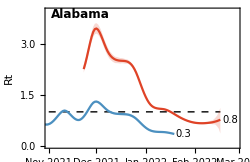
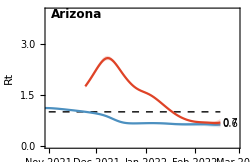
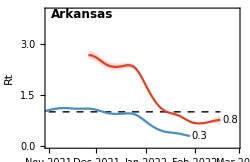
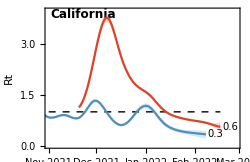
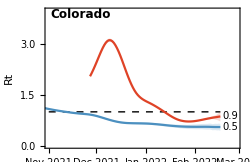
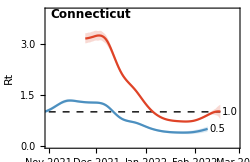
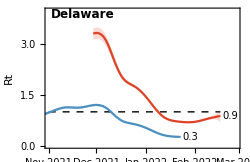
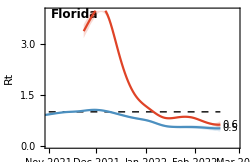
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-rt.png

Rt

```mathematica
Map[#->{rtGather[#,"Omicron"][[-1,1]],Round[rtGather[#,"Omicron"][[-1,2]],0.1],Round[rtGatherLower[#,"Omicron"][[-1,2]],0.1],Round[rtGatherUpper[#,"Omicron"][[-1,2]],0.1]}&,states]
```

{Alabama→{2022-02-17,0.8,0.4,1.1},Arizona→{2022-02-17,0.7,0.6,0.8},Arkansas→{2022-02-17,0.8,0.6,0.9},California→{2022-02-17,0.6,0.4,0.7},Colorado→{2022-02-17,0.9,0.7,1.},Connecticut→{2022-02-17,1.,0.8,1.2},Delaware→{2022-02-17,0.9,0.7,1.1},Florida→{2022-02-17,0.6,0.5,0.7},Georgia→{2022-02-17,0.7,0.5,0.9},Hawaii→{2022-02-17,0.7,0.6,0.9},Illinois→{2022-02-17,0.6,0.5,0.8},Indiana→{2022-02-17,0.5,0.4,0.7},Kentucky→{2022-02-17,1.2,0.9,1.4},Louisiana→{2022-02-17,0.7,0.6,0.9},Maryland→{2022-02-17,1.,0.8,1.1},Massachusetts→{2022-02-17,0.9,0.7,1.1},Michigan→{2022-02-17,0.9,0.7,1.1},Minnesota→{2022-02-17,0.6,0.5,0.7},Nebraska→{2022-02-17,0.6,0.5,0.6},Nevada→{2022-02-17,0.6,0.4,0.7},New Hampshire→{2022-02-17,0.7,0.3,1.1},New Jersey→{2022-02-17,1.2,0.9,1.4},New Mexico→{2022-02-17,0.7,0.5,0.9},New York→{2022-02-17,0.9,0.7,1.},North Carolina→{2022-02-17,0.,0.,0.1},North Dakota→{2022-02-17,0.6,0.5,0.7},Ohio→{2022-02-17,0.8,0.6,0.9},Oklahoma→{2022-02-17,0.3,0.1,0.5},Oregon→{2022-02-17,0.7,0.6,0.8},Pennsylvania→{2022-02-17,0.7,0.6,0.8},South Carolina→{2022-02-17,0.7,0.6,0.8},Tennessee→{2022-02-17,0.8,0.6,0.9},Texas→{2022-02-17,0.7,0.4,0.9},Utah→{2022-02-17,0.8,0.6,0.9},Vermont→{2022-02-17,0.5,0.3,0.7},Virginia→{2022-02-17,0.8,0.7,0.9},Wisconsin→{2022-02-17,0.8,0.6,0.9}}

## Little r estimates

Using fixed growth model

```mathematica
rData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_little-r-combined-"<>model<>".tsv"];
```

```mathematica
header=rData[[1]]
```

{date,location,variant,median_r,median_freq,r_upper_95,r_lower_95,r_upper_80,r_lower_80,r_upper_50,r_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_r→4,median_freq→5,r_upper_95→6,r_lower_95→7,r_upper_80→8,r_lower_80→9,r_upper_50→10,r_lower_50→11}

```mathematica
rData=Drop[rData,1];
```

Only keep Rt data points when the variant is frequent enough to have a good estimate

```mathematica
rData=Cases[rData,x_/;x[[5]]>0.001];
```

```mathematica
rGather[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
rGatherLower[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,9}]]
```

```mathematica
rGatherUpper[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
variantCountryLittleRPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=rGather[country,variant];
lowerSeries=rGatherLower[country,variant];
upperSeries=rGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{45,5},{15,10}},Joined->True,PlotRange->{{startDate,DatePlus[modelEndDate,7]},
{-0.35,0.5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,0}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
variantsCountryLittleRLabelPlot[country_,variants_]:=Module[{medians,finalDates,finalValues},
medians=Map[Last[rGather[country,#]]&,variants];
finalDates=medians[[All,1]];
finalValues=medians[[All,2]];
DateListPlot[{},Frame->{True,True,False,False},FrameLabel->{"","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{42,5},{15,10}},PlotRange->{{startDate,DatePlus[modelEndDate,15]},
{-0.35,0.5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Prolog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],MapThread[Text[Style[NumberForm[Round[#2,0.01],{2,2}],Black,FontSize->10,FontFamily->"Helvetica"],{DatePlus[#1,1],#2},{-1,0}]&,{finalDates,finalValues}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
countryLittleRPlot[country_]:=Show[variantsCountryLittleRLabelPlot[country,variants[[2;;3]]],Table[variantCountryLittleRPlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryLittleRPlot,states];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

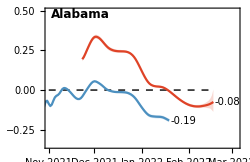
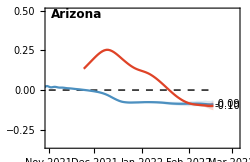
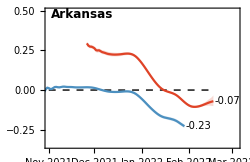
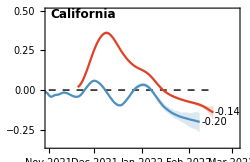
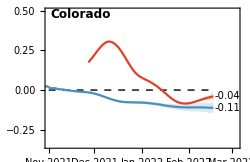
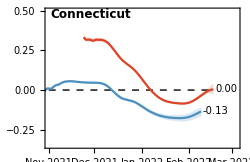
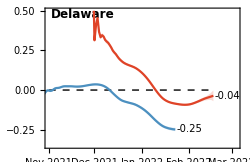
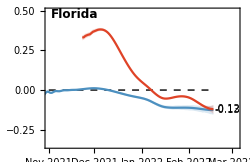
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-little-r.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-little-r.png

Little r

```mathematica
Map[#->{rGather[#,"Omicron"][[-1,1]],Round[rGather[#,"Omicron"][[-1,2]],0.01],Round[rGatherLower[#,"Omicron"][[-1,2]],0.01],Round[rGatherUpper[#,"Omicron"][[-1,2]],0.01]}&,states]
```

{Alabama→{2022-02-17,-0.08,-0.14,0.},Arizona→{2022-02-17,-0.1,-0.13,-0.07},Arkansas→{2022-02-17,-0.07,-0.1,-0.03},California→{2022-02-17,-0.14,-0.19,-0.1},Colorado→{2022-02-17,-0.04,-0.07,-0.01},Connecticut→{2022-02-17,0.,-0.03,0.04},Delaware→{2022-02-17,-0.04,-0.07,0.},Florida→{2022-02-17,-0.12,-0.15,-0.09},Georgia→{2022-02-17,-0.08,-0.12,-0.05},Hawaii→{2022-02-17,-0.08,-0.12,-0.05},Illinois→{2022-02-17,-0.1,-0.14,-0.06},Indiana→{2022-02-17,-0.14,-0.17,-0.1},Kentucky→{2022-02-17,0.03,-0.01,0.06},Louisiana→{2022-02-17,-0.08,-0.12,-0.06},Maryland→{2022-02-17,-0.02,-0.05,0.01},Massachusetts→{2022-02-17,-0.03,-0.06,0.},Michigan→{2022-02-17,-0.04,-0.08,0.},Minnesota→{2022-02-17,-0.11,-0.13,-0.08},Nebraska→{2022-02-17,-0.14,-0.17,-0.12},Nevada→{2022-02-17,-0.13,-0.17,-0.1},New Hampshire→{2022-02-17,-0.03,-0.11,0.06},New Jersey→{2022-02-17,0.03,0.,0.06},New Mexico→{2022-02-17,-0.07,-0.11,-0.03},New York→{2022-02-17,-0.05,-0.08,-0.02},North Carolina→{2022-02-17,-0.38,-0.49,-0.27},North Dakota→{2022-02-17,-0.11,-0.15,-0.08},Ohio→{2022-02-17,-0.07,-0.1,-0.04},Oklahoma→{2022-02-17,-0.27,-0.35,-0.2},Oregon→{2022-02-17,-0.08,-0.11,-0.06},Pennsylvania→{2022-02-17,-0.08,-0.11,-0.06},South Carolina→{2022-02-17,-0.08,-0.11,-0.06},Tennessee→{2022-02-17,-0.07,-0.1,-0.04},Texas→{2022-02-17,-0.1,-0.14,-0.05},Utah→{2022-02-17,-0.07,-0.11,-0.04},Vermont→{2022-02-17,-0.16,-0.22,-0.08},Virginia→{2022-02-17,-0.06,-0.08,-0.04},Wisconsin→{2022-02-17,-0.07,-0.11,-0.04}}

Doubling time

```mathematica
Map[#->{rGather[#,"Omicron"][[-1,1]],Round[Log[2]/rGather[#,"Omicron"][[-1,2]],0.1],Round[Log[2]/rGatherUpper[#,"Omicron"][[-1,2]],0.1],Round[Log[2]/rGatherLower[#,"Omicron"][[-1,2]],0.1]}&,states]
```

{Alabama→{2022-02-17,-9.2,256.6,-5.},Arizona→{2022-02-17,-7.,-9.9,-5.4},Arkansas→{2022-02-17,-9.8,-20.2,-6.9},California→{2022-02-17,-4.9,-7.1,-3.6},Colorado→{2022-02-17,-17.3,-61.1,-10.},Connecticut→{2022-02-17,169.2,15.8,-22.9},Delaware→{2022-02-17,-19.2,-286.4,-9.8},Florida→{2022-02-17,-5.8,-7.3,-4.6},Georgia→{2022-02-17,-8.4,-14.6,-5.6},Hawaii→{2022-02-17,-8.5,-14.5,-6.},Illinois→{2022-02-17,-7.2,-11.7,-5.1},Indiana→{2022-02-17,-5.,-6.9,-4.},Kentucky→{2022-02-17,24.4,10.7,-84.4},Louisiana→{2022-02-17,-8.2,-12.3,-6.},Maryland→{2022-02-17,-40.4,52.7,-14.7},Massachusetts→{2022-02-17,-24.9,207.8,-10.7},Michigan→{2022-02-17,-18.1,-5118.4,-8.5},Minnesota→{2022-02-17,-6.6,-8.9,-5.2},Nebraska→{2022-02-17,-4.8,-5.9,-4.},Nevada→{2022-02-17,-5.2,-6.8,-4.},New Hampshire→{2022-02-17,-26.7,12.,-6.5},New Jersey→{2022-02-17,20.5,11.,103831.},New Mexico→{2022-02-17,-9.9,-25.,-6.5},New York→{2022-02-17,-14.9,-37.3,-9.2},North Carolina→{2022-02-17,-1.8,-2.6,-1.4},North Dakota→{2022-02-17,-6.,-8.4,-4.7},Ohio→{2022-02-17,-10.6,-18.,-7.2},Oklahoma→{2022-02-17,-2.6,-3.5,-2.},Oregon→{2022-02-17,-8.5,-11.9,-6.3},Pennsylvania→{2022-02-17,-8.4,-11.4,-6.6},South Carolina→{2022-02-17,-8.2,-12.2,-6.2},Tennessee→{2022-02-17,-10.5,-17.8,-7.3},Texas→{2022-02-17,-7.2,-15.1,-4.8},Utah→{2022-02-17,-9.6,-17.5,-6.4},Vermont→{2022-02-17,-4.4,-8.7,-3.1},Virginia→{2022-02-17,-11.7,-18.9,-8.6},Wisconsin→{2022-02-17,-9.3,-15.8,-6.3}}

## Prevalence

Using fixed growth model

```mathematica
pData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_I-combined-"<>model<>".tsv"];
```

```mathematica
header=pData[[1]]
```

{date,location,variant,median_I,I_upper_95,I_lower_95,I_upper_80,I_lower_80,I_upper_50,I_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_I→4,I_upper_95→5,I_lower_95→6,I_upper_80→7,I_lower_80→8,I_upper_50→9,I_lower_50→10}

```mathematica
pData=Drop[pData,1];
```

Only keep data points with incidence

```mathematica
pData=Cases[pData,x_/;x[[4]]>0.9];
```

```mathematica
pGather[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
pGatherLower[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
pGatherUpper[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListLogPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{20,240000}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryPrevalencePlot,states];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

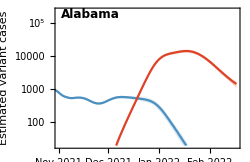
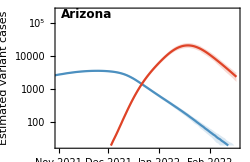
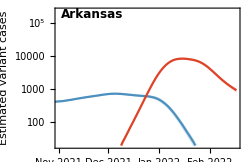
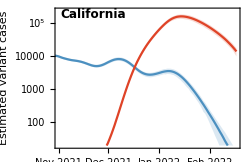
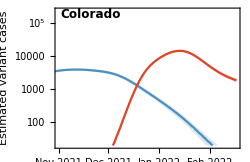
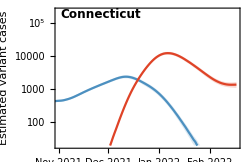
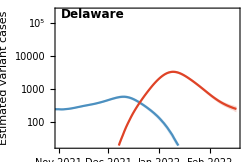
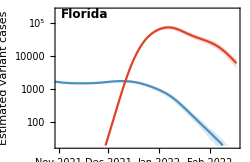
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-estimated-log-cases.png

```mathematica
yMaxForCountry[country_]:=Max[Flatten[Table[pGatherUpper[country,variant][[All,2]],{variant,variants}]]]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,yMaxForCountry[country]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryPrevalencePlot,states];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

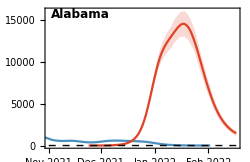
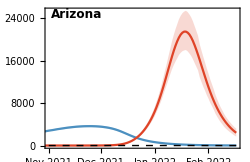
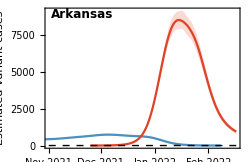
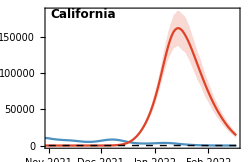
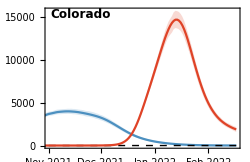
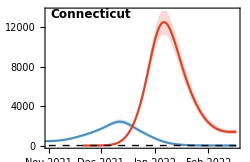
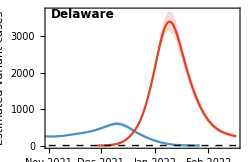
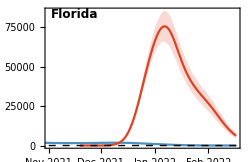
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-estimated-cases.png

Prevalence

```mathematica
Map[#->{pGather[#,"Omicron"][[-1,1]],Round[pGather[#,"Omicron"][[-1,2]]],Round[pGatherLower[#,"Omicron"][[-1,2]]],Round[pGatherUpper[#,"Omicron"][[-1,2]]]}&,states]
```

{Alabama→{2022-02-17,1462,1107,1817},Arizona→{2022-02-17,2410,1695,3187},Arkansas→{2022-02-17,944,791,1087},California→{2022-02-17,14131,9942,17798},Colorado→{2022-02-17,1883,1582,2173},Connecticut→{2022-02-17,1398,1113,1691},Delaware→{2022-02-17,256,203,314},Florida→{2022-02-17,6193,4246,8021},Georgia→{2022-02-17,2774,2316,3273},Hawaii→{2022-02-17,419,333,504},Illinois→{2022-02-17,3343,2703,4044},Indiana→{2022-02-17,1519,1299,1740},Kentucky→{2022-02-17,3459,3041,3905},Louisiana→{2022-02-17,1679,1288,2048},Maryland→{2022-02-17,838,608,1068},Massachusetts→{2022-02-17,1698,1266,2102},Michigan→{2022-02-17,3533,2770,4240},Minnesota→{2022-02-17,2136,1764,2461},Nebraska→{2022-02-17,182,117,241},Nevada→{2022-02-17,618,521,713},New Hampshire→{2022-02-17,1972,1413,2636},New Jersey→{2022-02-17,1695,1419,1964},New Mexico→{2022-02-17,1310,1010,1587},New York→{2022-02-17,3295,2614,3982},North Carolina→{2022-02-17,4632,3560,5663},North Dakota→{2022-02-17,334,258,415},Ohio→{2022-02-17,1788,1522,2026},Oklahoma→{2022-02-17,1263,952,1557},Oregon→{2022-02-17,1531,906,2203},Pennsylvania→{2022-02-17,2243,1848,2561},South Carolina→{2022-02-17,1600,1243,1918},Tennessee→{2022-02-17,2838,2415,3260},Texas→{2022-02-17,7640,5903,9217},Utah→{2022-02-17,1079,721,1409},Vermont→{2022-02-17,407,277,514},Virginia→{2022-02-17,3084,2693,3421},Wisconsin→{2022-02-17,1690,1443,1901}}

## Frequency

```mathematica
fData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_freq-combined-"<>model<>".tsv"];
```

```mathematica
header=fData[[1]]
```

{date,location,variant,median_freq,freq_upper_95,freq_lower_95,freq_upper_80,freq_lower_80,freq_upper_50,freq_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_freq→4,freq_upper_95→5,freq_lower_95→6,freq_upper_80→7,freq_lower_80→8,freq_upper_50→9,freq_lower_50→10}

```mathematica
fData=Drop[fData,1];
```

```mathematica
fGather[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
fGatherLower[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
fGatherUpper[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryFrequencyPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=fGather[country,variant];
lowerSeries=fGatherLower[country,variant];
upperSeries=fGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated Omicron frequency"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,1}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Table[{i,ToString[Round[100*i]]<>"%"},{i,0,1,0.2}],Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{endDate,0}}]}]
]
```

```mathematica
countryFrequencyPlot[country_]:=variantCountryFrequencyPlot[country,variants[[3]],colors[[3]]]
```

```mathematica
panels=Map[countryFrequencyPlot,states];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

```mathematica
fig=Grid[gappedPartition[panels,gridCount],Spacings->{1,1},Alignment->Right]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-frequency.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-estimated-frequency.png

Frequency

```mathematica
Map[#->{fGather[#,"Omicron"][[-1,1]],Round[fGather[#,"Omicron"][[-1,2]],0.01],Round[fGatherLower[#,"Omicron"][[-1,2]],0.01],Round[fGatherUpper[#,"Omicron"][[-1,2]],0.01]}&,states]
```

{Alabama→{2022-02-17,1.,1.,1.},Arizona→{2022-02-17,0.99,0.99,1.},Arkansas→{2022-02-17,1.,1.,1.},California→{2022-02-17,1.,1.,1.},Colorado→{2022-02-17,1.,1.,1.},Connecticut→{2022-02-17,1.,1.,1.},Delaware→{2022-02-17,1.,1.,1.},Florida→{2022-02-17,1.,1.,1.},Georgia→{2022-02-17,1.,1.,1.},Hawaii→{2022-02-17,1.,1.,1.},Illinois→{2022-02-17,1.,1.,1.},Indiana→{2022-02-17,1.,1.,1.},Kentucky→{2022-02-17,1.,1.,1.},Louisiana→{2022-02-17,1.,1.,1.},Maryland→{2022-02-17,1.,1.,1.},Massachusetts→{2022-02-17,1.,1.,1.},Michigan→{2022-02-17,1.,1.,1.},Minnesota→{2022-02-17,1.,1.,1.},Nebraska→{2022-02-17,0.81,0.73,0.89},Nevada→{2022-02-17,1.,1.,1.},New Hampshire→{2022-02-17,1.,1.,1.},New Jersey→{2022-02-17,1.,1.,1.},New Mexico→{2022-02-17,1.,1.,1.},New York→{2022-02-17,1.,1.,1.},North Carolina→{2022-02-17,1.,1.,1.},North Dakota→{2022-02-17,1.,1.,1.},Ohio→{2022-02-17,1.,1.,1.},Oklahoma→{2022-02-17,1.,1.,1.},Oregon→{2022-02-17,0.97,0.96,0.99},Pennsylvania→{2022-02-17,0.96,0.95,0.98},South Carolina→{2022-02-17,1.,1.,1.},Tennessee→{2022-02-17,1.,1.,1.},Texas→{2022-02-17,1.,1.,1.},Utah→{2022-02-17,1.,1.,1.},Vermont→{2022-02-17,1.,1.,1.},Virginia→{2022-02-17,1.,1.,1.},Wisconsin→{2022-02-17,1.,1.,1.}}

## Phase diagrams

Convert to cases per 100k per day

```mathematica
perCapitaPGather[state_,variant_]:=Module[{popSize,stateName},
stateName=StringReplace[state," "->""];
popSize=QuantityMagnitude[AdministrativeDivisionData[{stateName, "UnitedStates"},"Population"]];
Map[{#[[1]],100000*#[[2]]/popSize}&,pGather[state,variant]]
]
```

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
phaseGather[country_,variant_]:=compareWithDate[perCapitaPGather[country,variant],rGather[country,variant]][[All,{2,3}]]
```

```mathematica
countryRPrevalencePhasePlot[country_]:=Module[{pairsOmicron},
pairsOmicron=phaseGather[country,"Omicron"];
ListLogLinearPlot[{pairsOmicron,{Last[pairsOmicron]}},Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->True,PlotRange->{{2,650},
{-0.25,0.45}},Joined->{True,False},PlotMarkers->{None,{"•",Scaled[0.12]}},PlotStyle->{colors[[3]],colors[[3]]},
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
panels=Map[countryRPrevalencePhasePlot,states];
```

```mathematica
fig=Grid[gappedPartition[panels,gridCount],Spacings->{1,1},Alignment->Right]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
Export["figures/"<>dataset<>"_variant-cases-vs-rt.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-cases-vs-rt.png

```mathematica
stateLines=Map[With[{pairs=phaseGather[#,"Omicron"]},pairs]&,states];
```

```mathematica
figLines=ListLogLinearPlot[stateLines,Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->True,PlotRange->{{2,700},
{-0.25,0.4}},PlotStyle->Directive[colors[[3]],Opacity[0.5]],Prolog->{Dashed,Black,Line[{{0,0},{1000,0}}]}];
```

```mathematica
statePoints=Map[With[{pairs=phaseGather[#,"Omicron"]},Last[pairs]]&,states];
```

```mathematica
figPoints=ListLogLinearPlot[statePoints,Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{{2,150},
{-0.25,0.4}},PlotStyle->Directive[colors[[3]]],PlotMarkers->{"•",Scaled[0.1]}];
```

```mathematica
fig=Show[figLines,figPoints]
```

-Graphics-

```mathematica
Export["figures/"<>dataset<>"_variant-cases-vs-rt-overlay.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-cases-vs-rt-overlay.png

### Growth rate vs peak incidence

```mathematica
initialR[state_,variant_]:=Module[{pairs,sorted},
pairs=phaseGather[state,variant];
sorted=Sort[pairs,(#1[[1]]-10)^2<(#2[[1]]-10)^2&];
sorted[[1,2]]
]
```

```mathematica
initialR["Washington","Omicron"]
```

0.177055

```mathematica
peakIncidence[state_,variant_]:=Module[{pairs,sorted},
pairs=phaseGather[state,variant];
sorted=Sort[pairs,#1[[1]]>#2[[1]]&];
sorted[[1,1]]
]
```

```mathematica
peakIncidence["Washington","Omicron"]
```

8406.77

```mathematica
pairs=Map[{initialR[#,"Omicron"],peakIncidence[#,"Omicron"]}&,states];
```

```mathematica
ListPlot[pairs,Frame->{True,True,False,False},FrameLabel->{"Initial epidemic growth rate r","Peak cases per 100k per day"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{All,
All},PlotStyle->Directive[colors[[3]]],PlotMarkers->{"•",Scaled[0.1]},Epilog->{Text[Style["corr = "<>ToString[Round[Correlation[pairs[[All,1]],pairs[[All,2]]],0.01]],Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
```

-Graphics-

```mathematica
rValues=Map[initialR[#,"Omicron"]&,states]
```

{0.244369,0.206139,0.229229,0.270594,0.285686,0.274923,0.249315,0.336887,0.233527,0.232788,0.235677,0.192966,0.209628,0.171786,0.253171,0.290219,0.230211,0.167774,0.210731,0.219709,0.2271,0.240539,0.185292,0.265031,0.232662,0.158843,0.204931,0.168414,0.219608,0.201203,0.206942,0.18145,0.173447,0.228957,0.173986,0.237888,0.233004}

```mathematica
baseColorFunction[t_]:=Blend[{Lighter[ColorData["Rainbow"][0.75],0.4],Lighter[ColorData["Rainbow"][0.75],0.05],RGBColor[0.5807,0.6182,0.4944],Darker[ColorData["Rainbow"][0.3],0.05],Darker[ColorData["Rainbow"][0.3],0.4],GrayLevel[0.05]},t]
```

```mathematica
baseColorFunction[t_]:=Blend[{Lighter[ColorData["Rainbow"][0.15],0.0],Lighter[ColorData["Rainbow"][0.3],0.0],Lighter[ColorData["Rainbow"][0.7],0.0],Lighter[ColorData["Rainbow"][0.9],0.0]},t]
```

```mathematica
standardizedColorFunction[t_,min_,max_]:=baseColorFunction[(t-min)/(max-min)]
```

```mathematica
phaseColors=Map[standardizedColorFunction[#,Min[rValues],Max[rValues]]&,rValues]
```

{RGBColor[0.5230873647163158, 0.62987875454885, 0.5333388546126094],RGBColor[0.28782822446877343, 0.5077014111564655, 0.7594854329528182],RGBColor[0.39288394943757887, 0.5928144228162769, 0.6599402735402082],RGBColor[0.7486114651326388, 0.6940775319282769, 0.3140537379053872],RGBColor[0.8199562569693564, 0.6669600579032351, 0.24546467573115402],RGBColor[0.7858396162660403, 0.7046750768578384, 0.2778554803754296],RGBColor[0.565615739022613, 0.6419850865522092, 0.49198700128115136],RGBColor[0.8929546, 0.38966159999999994, 0.1794008],RGBColor[0.4298497209483738, 0.6033372774978804, 0.6239971370640923],RGBColor[0.42348957353797256, 0.6015267672821343, 0.6301813349595294],RGBColor[0.4483377235794005, 0.6086001614331603, 0.6060205935055809],RGBColor[0.2767539106273845, 0.4442033925949549, 0.7674067366522291],RGBColor[0.2907610524960493, 0.5245176917117153, 0.7573876215818446],RGBColor[0.25894930296718977, 0.34211514370840646, 0.7801421265414119],RGBColor[0.5987780809794806, 0.6514252386456627, 0.45974207485035207],RGBColor[0.8264190485253016, 0.6424098824086849, 0.23961581614746333],RGBColor[0.4013252462636093, 0.5952173630551587, 0.6517324999309164],RGBColor[0.25557653980742795, 0.32277635840852414, 0.7825546174349612],RGBColor[0.2916886210000238, 0.5298361938713994, 0.7567241446452844],RGBColor[0.3110135093786408, 0.5695087887594431, 0.7395458188901477],RGBColor[0.3745763704211799, 0.5876028991367217, 0.6777413847909648],RGBColor[0.4901505092787782, 0.6205027905347628, 0.5653645324681306],RGBColor[0.270303207173575, 0.40721628048025726, 0.7720208357164521],RGBColor[0.7007768477997641, 0.6804606992105572, 0.36056504035652653],RGBColor[0.422411073751964, 0.6012197563350208, 0.6312299987209945],RGBColor[0.2480688, 0.2797284, 0.7879248],RGBColor[0.2868126655757188, 0.501878388767441, 0.7602118481991026],RGBColor[0.25611488933610776, 0.3258631526654226, 0.7821695434543802],RGBColor[0.31014209255927827, 0.5692607270476896, 0.7403931285062011],RGBColor[0.28367841042388486, 0.4839071632217237, 0.7624537376095625],RGBColor[0.28850345634247965, 0.511573062860039, 0.7590024489218655],RGBColor[0.2670737572987122, 0.3886992264185325, 0.7743308165971822],RGBColor[0.26034547262321295, 0.35012051614076833, 0.7791434656745031],RGBColor[0.3905445482990099, 0.5921484776129975, 0.6622149566040099],RGBColor[0.26079863111311014, 0.352718841112854, 0.7788193276670514],RGBColor[0.4673485935016267, 0.6140118872916084, 0.5875356474536713],RGBColor[0.4253471283882866, 0.6020555477986522, 0.628375168206667]}

```mathematica
Min[rValues]
```

0.158843

```mathematica
Max[rValues]
```

0.336887

```mathematica
legend=PointLegend[Table[standardizedColorFunction[i,Min[rValues],Max[rValues]],{i,0.15,0.3,0.05}],Table["initial r = "<>ToString[NumberForm[Round[i,0.01],{3,2}]],{i,0.15,0.3,0.05}],LegendMarkerSize->20,LegendLayout->{"Column",1},Spacings->{0,1}]
```

```mathematica
figLines=ListLogLinearPlot[stateLines,Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->True,PlotRange->{{3,600},
{-0.25,0.4}},PlotStyle->Map[Directive[#,Opacity[0.5]]&,phaseColors],PlotLegends->Placed[legend,Right]]
```

-Graphics-

```mathematica
figPoints=ListLogLinearPlot[Map[{#}&,statePoints],Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{All,
All},PlotStyle->phaseColors,PlotMarkers->{"•",Scaled[0.1]}]
```

-Graphics-

```mathematica
fig=Show[figLines,figPoints]
```

-Graphics-

### Mapping

```mathematica
mapFig=Module[{entities},
GeoGraphics[{Map[{GeoStyling[Opacity@1,EdgeForm[GrayLevel[0.8]],FaceForm[GrayLevel[0.9]]],Polygon@#}&,EntityList[EntityClass["AdministrativeDivision","ContinentalUSStates"]]]},GeoRangePadding->None,GeoRange->{{25,49},{-125,-67}},GeoBackground->None,ImageSize->400,ImageMargins->0]
]
```

-Graphics-

```mathematica
fullStateNamesToAbbreviations={"Alaska"->"AK","Washington"->"WA","Idaho"->"ID","Montana"->"MT","Oregon"->"OR","Nevada"->"NV","Wyoming"->"WY","California"->"CA","Utah"->"UT","Colorado"->"CO","Hawaii"->"HI","Arizona"->"AZ","New Mexico"->"NM","Oklahoma"->"OK","Texas"->"TX","North Dakota"->"ND","Minnesota"->"MN","Illinois"->"IL","Wisconsin"->"WI","Michigan"->"MI","South Dakota"->"SD","Iowa"->"IA","Indiana"->"IN","Ohio"->"OH","Nebraska"->"NE","Missouri"->"MO","Kansas"->"KS","Kentucky"->"KY","West Virginia"->"WV","Virginia"->"VA","Arkansas"->"AR","Tennessee"->"TN","North Carolina"->"NC","South Carolina"->"SC","Louisiana"->"LA","Mississippi"->"MS","Alabama"->"AL","Georgia"-> "GA","Florida"->"FL","Maine"->"ME","Vermont"->"VT","New Hampshire"->"NH","New York"->"NY","Massachusetts"->"MA","Rhode Island"->"RI","Pennsylvania"->"PA","New Jersey"->"NJ","Connecticut"-> "CT","Maryland"->"MD","Washington DC"->"DC","Delaware"->"DE"};
```

```mathematica
abbreviationsToFullStateNames=Map[#[[2]]->#[[1]]&,fullStateNamesToAbbreviations];
```

```mathematica
geoCasesPerCapita=DeleteCases[Map[#->With[{state=#[EntityProperty["AdministrativeDivision","StateAbbreviation"]]/.abbreviationsToFullStateNames},
If[MemberQ[states,state],peakIncidence[state,"Omicron"],Null]]&,EntityList[EntityClass["AdministrativeDivision","ContinentalUSStates"]]],x_/;x[[2]]==Null]
```

{Alabama, United States→288.426,Arizona, United States→300.157,Arkansas, United States→283.201,California, United States→410.923,Colorado, United States→254.247,Connecticut, United States→347.394,Delaware, United States→344.053,Florida, United States→349.709,Georgia, United States→239.696,Illinois, United States→285.313,Indiana, United States→256.72,Kentucky, United States→281.593,Louisiana, United States→405.28,Maryland, United States→253.376,Massachusetts, United States→346.145,Michigan, United States→333.048,Minnesota, United States→304.041,Nebraska, United States→219.423,Nevada, United States→347.535,New Hampshire, United States→491.049,New Jersey, United States→304.847,New Mexico, United States→544.66,New York, United States→343.316,North Carolina, United States→281.894,North Dakota, United States→312.299,Ohio, United States→217.117,Oklahoma, United States→404.742,Oregon, United States→248.921,Pennsylvania, United States→196.459,South Carolina, United States→319.784,Tennessee, United States→239.515,Texas, United States→234.847,Utah, United States→546.737,Vermont, United States→445.375,Virginia, United States→263.076,Wisconsin, United States→406.784}

```mathematica
geoColors=DeleteCases[Map[With[{state=#[EntityProperty["AdministrativeDivision","StateAbbreviation"]]/.abbreviationsToFullStateNames},
If[MemberQ[states,state],standardizedColorFunction[initialR[state,"Omicron"],Min[rValues],Max[rValues]],Null]]&,EntityList[EntityClass["AdministrativeDivision","ContinentalUSStates"]]],x_/;x==Null]
```

{RGBColor[0.5230873647163158, 0.62987875454885, 0.5333388546126094],RGBColor[0.28782822446877343, 0.5077014111564655, 0.7594854329528182],RGBColor[0.39288394943757887, 0.5928144228162769, 0.6599402735402082],RGBColor[0.7486114651326388, 0.6940775319282769, 0.3140537379053872],RGBColor[0.8199562569693564, 0.6669600579032351, 0.24546467573115402],RGBColor[0.7858396162660403, 0.7046750768578384, 0.2778554803754296],RGBColor[0.565615739022613, 0.6419850865522092, 0.49198700128115136],RGBColor[0.8929546, 0.38966159999999994, 0.1794008],RGBColor[0.4298497209483738, 0.6033372774978804, 0.6239971370640923],RGBColor[0.4483377235794005, 0.6086001614331603, 0.6060205935055809],RGBColor[0.2767539106273845, 0.4442033925949549, 0.7674067366522291],RGBColor[0.2907610524960493, 0.5245176917117153, 0.7573876215818446],RGBColor[0.25894930296718977, 0.34211514370840646, 0.7801421265414119],RGBColor[0.5987780809794806, 0.6514252386456627, 0.45974207485035207],RGBColor[0.8264190485253016, 0.6424098824086849, 0.23961581614746333],RGBColor[0.4013252462636093, 0.5952173630551587, 0.6517324999309164],RGBColor[0.25557653980742795, 0.32277635840852414, 0.7825546174349612],RGBColor[0.2916886210000238, 0.5298361938713994, 0.7567241446452844],RGBColor[0.3110135093786408, 0.5695087887594431, 0.7395458188901477],RGBColor[0.3745763704211799, 0.5876028991367217, 0.6777413847909648],RGBColor[0.4901505092787782, 0.6205027905347628, 0.5653645324681306],RGBColor[0.270303207173575, 0.40721628048025726, 0.7720208357164521],RGBColor[0.7007768477997641, 0.6804606992105572, 0.36056504035652653],RGBColor[0.422411073751964, 0.6012197563350208, 0.6312299987209945],RGBColor[0.2480688, 0.2797284, 0.7879248],RGBColor[0.2868126655757188, 0.501878388767441, 0.7602118481991026],RGBColor[0.25611488933610776, 0.3258631526654226, 0.7821695434543802],RGBColor[0.31014209255927827, 0.5692607270476896, 0.7403931285062011],RGBColor[0.28367841042388486, 0.4839071632217237, 0.7624537376095625],RGBColor[0.28850345634247965, 0.511573062860039, 0.7590024489218655],RGBColor[0.2670737572987122, 0.3886992264185325, 0.7743308165971822],RGBColor[0.26034547262321295, 0.35012051614076833, 0.7791434656745031],RGBColor[0.3905445482990099, 0.5921484776129975, 0.6622149566040099],RGBColor[0.26079863111311014, 0.352718841112854, 0.7788193276670514],RGBColor[0.4673485935016267, 0.6140118872916084, 0.5875356474536713],RGBColor[0.4253471283882866, 0.6020555477986522, 0.628375168206667]}

```mathematica
bubbleFig=GeoBubbleChart[geoCasesPerCapita,ChartStyle->geoColors,GeoRange->{{25,50},{-125,-67}},BubbleSizes->Medium,ColorFunctionScaling->True]
```

-Graphics-

```mathematica
fig=Show[mapFig,bubbleFig]
```

-Graphics-

### Parallel epidemics

```mathematica
translatedSeries[country_,variant_]:=Module[{series,sorted,initialDate},
series=perCapitaPGather[country,variant];
sorted=Sort[series,(#1[[2]]-10)^2<(#2[[2]]-10)^2&];
initialDate=sorted[[1,1]];
Map[{QuantityMagnitude[DateDifference[initialDate,#[[1]]]],#[[2]]}&,series]
]
```

```mathematica
translatedSeries["Washington","Omicron"]
```

{{-26,0.0129602},{-25,0.0129602},{-24,0.0129602},{-23,0.0129602},{-22,0.0259203},{-21,0.0259203},{-20,0.0259203},{-19,0.0388805},{-18,0.0518407},{-17,0.0648009},{-16,0.077761},{-15,0.116642},{-14,0.155522},{-13,0.233283},{-12,0.349925},{-11,0.505447},{-10,0.73873},{-9,1.06273},{-8,1.49042},{-7,2.03475},{-6,2.69572},{-5,3.49925},{-4,4.41942},{-3,5.48215},{-2,6.68745},{-1,8.07419},{0,9.62941},{1,11.405},{2,13.4527},{3,15.7855},{4,18.4812},{5,21.6305},{6,25.2335},{7,29.3548},{8,34.0334},{9,39.36},{10,45.3476},{11,52.0999},{12,59.7075},{13,68.0928},{14,77.3852},{15,87.5589},{16,98.4714},{17,110.174},{18,122.564},{19,135.589},{20,149.418},{21,163.868},{22,178.98},{23,194.714},{24,211.251},{25,228.475},{26,246.503},{27,265.645},{28,285.668},{29,306.534},{30,328.165},{31,349.717},{32,370.998},{33,391.488},{34,410.954},{35,427.997},{36,441.955},{37,452.569},{38,459.062},{39,460.371},{40,457.352},{41,450.418},{42,438.507},{43,423.059},{44,404.293},{45,383.038},{46,359.982},{47,335.785},{48,311.368},{49,287.755},{50,265.139},{51,244.312},{52,224.989},{53,207.739},{54,193.923},{55,183.879},{56,179.991},{57,181.792},{58,192.899},{59,219.105},{60,269.792},{61,369.391},{62,560.657},{63,954.698},{64,1790.15},{65,3729.34},{66,8406.77}}

```mathematica
tSeries=Map[translatedSeries[#,"Omicron"]&,states];
```

```mathematica
variantCountryTranslatedPrevalencePlot[country_,variant_,color_]:=Module[{series},
series=translatedSeries[country,variant];
ListLogPlot[series,Frame->{True,True,False,False},FrameLabel->{"Days since 10 cases per 100k","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{55,5},{32,10}},Joined->True,PlotRange->{{-3,All},
{4,500}},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{{10,20,50,100,200,500,1000},Automatic},{Automatic,Automatic}}]
]
```

```mathematica
variantCountryTranslatedPrevalencePlot[country_,variant_,color_]:=Module[{series},
series=translatedSeries[country,variant];
ListPlot[series,Frame->{True,True,False,False},FrameLabel->{"Days since 10 cases per 100k","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{55,5},{32,10}},Joined->True,PlotRange->{{-3,All},
{0,500}},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}}]
]
```

```mathematica
panels=MapThread[variantCountryTranslatedPrevalencePlot[#1,"Omicron",#2]&,{states,phaseColors}];
```

```mathematica
fig=Show[panels]
```

-Graphics-

## Vaccination data

Download at https://data.cdc.gov/api/views/unsk-b7fc/rows.csv?accessType=DOWNLOAD

### Import data

```mathematica
vacData=Import["https://data.cdc.gov/api/views/unsk-b7fc/rows.csv?accessType=DOWNLOAD"];
```

```mathematica
vacHeader=vacData[[1]]
```

{Date,MMWR_week,Location,Distributed,Distributed_Janssen,Distributed_Moderna,Distributed_Pfizer,Distributed_Unk_Manuf,Dist_Per_100K,Distributed_Per_100k_12Plus,Distributed_Per_100k_18Plus,Distributed_Per_100k_65Plus,Administered,Administered_12Plus,Administered_18Plus,Administered_65Plus,Administered_Janssen,Administered_Moderna,Administered_Pfizer,Administered_Unk_Manuf,Admin_Per_100K,Admin_Per_100k_12Plus,Admin_Per_100k_18Plus,Admin_Per_100k_65Plus,Recip_Administered,Administered_Dose1_Recip,Administered_Dose1_Pop_Pct,Administered_Dose1_Recip_12Plus,Administered_Dose1_Recip_12PlusPop_Pct,Administered_Dose1_Recip_18Plus,Administered_Dose1_Recip_18PlusPop_Pct,Administered_Dose1_Recip_65Plus,Administered_Dose1_Recip_65PlusPop_Pct,Series_Complete_Yes,Series_Complete_Pop_Pct,Series_Complete_12Plus,Series_Complete_12PlusPop_Pct,Series_Complete_18Plus,Series_Complete_18PlusPop_Pct,Series_Complete_65Plus,Series_Complete_65PlusPop_Pct,Series_Complete_Janssen,Series_Complete_Moderna,Series_Complete_Pfizer,Series_Complete_Unk_Manuf,Series_Complete_Janssen_12Plus,Series_Complete_Moderna_12Plus,Series_Complete_Pfizer_12Plus,Series_Complete_Unk_Manuf_12Plus,Series_Complete_Janssen_18Plus,Series_Complete_Moderna_18Plus,Series_Complete_Pfizer_18Plus,Series_Complete_Unk_Manuf_18Plus,Series_Complete_Janssen_65Plus,Series_Complete_Moderna_65Plus,Series_Complete_Pfizer_65Plus,Series_Complete_Unk_Manuf_65Plus,Additional_Doses,Additional_Doses_Vax_Pct,Additional_Doses_12Plus,Additional_Doses_12Plus_Vax_Pct,Additional_Doses_18Plus,Additional_Doses_18Plus_Vax_Pct,Additional_Doses_50Plus,Additional_Doses_50Plus_Vax_Pct,Additional_Doses_65Plus,Additional_Doses_65Plus_Vax_Pct,Additional_Doses_Moderna,Additional_Doses_Pfizer,Additional_Doses_Janssen,Additional_Doses_Unk_Manuf,Administered_Dose1_Recip_5Plus,Administered_Dose1_Recip_5PlusPop_Pct,Series_Complete_5Plus,Series_Complete_5PlusPop_Pct,Administered_5Plus,Admin_Per_100k_5Plus,Distributed_Per_100k_5Plus,Series_Complete_Moderna_5Plus,Series_Complete_Pfizer_5Plus,Series_Complete_Janssen_5Plus,Series_Complete_Unk_Manuf_5Plus}

```mathematica
vacHeaderRules=MapIndexed[#1->#2[[1]]&,vacHeader]
```

{Date→1,MMWR_week→2,Location→3,Distributed→4,Distributed_Janssen→5,Distributed_Moderna→6,Distributed_Pfizer→7,Distributed_Unk_Manuf→8,Dist_Per_100K→9,Distributed_Per_100k_12Plus→10,Distributed_Per_100k_18Plus→11,Distributed_Per_100k_65Plus→12,Administered→13,Administered_12Plus→14,Administered_18Plus→15,Administered_65Plus→16,Administered_Janssen→17,Administered_Moderna→18,Administered_Pfizer→19,Administered_Unk_Manuf→20,Admin_Per_100K→21,Admin_Per_100k_12Plus→22,Admin_Per_100k_18Plus→23,Admin_Per_100k_65Plus→24,Recip_Administered→25,Administered_Dose1_Recip→26,Administered_Dose1_Pop_Pct→27,Administered_Dose1_Recip_12Plus→28,Administered_Dose1_Recip_12PlusPop_Pct→29,Administered_Dose1_Recip_18Plus→30,Administered_Dose1_Recip_18PlusPop_Pct→31,Administered_Dose1_Recip_65Plus→32,Administered_Dose1_Recip_65PlusPop_Pct→33,Series_Complete_Yes→34,Series_Complete_Pop_Pct→35,Series_Complete_12Plus→36,Series_Complete_12PlusPop_Pct→37,Series_Complete_18Plus→38,Series_Complete_18PlusPop_Pct→39,Series_Complete_65Plus→40,Series_Complete_65PlusPop_Pct→41,Series_Complete_Janssen→42,Series_Complete_Moderna→43,Series_Complete_Pfizer→44,Series_Complete_Unk_Manuf→45,Series_Complete_Janssen_12Plus→46,Series_Complete_Moderna_12Plus→47,Series_Complete_Pfizer_12Plus→48,Series_Complete_Unk_Manuf_12Plus→49,Series_Complete_Janssen_18Plus→50,Series_Complete_Moderna_18Plus→51,Series_Complete_Pfizer_18Plus→52,Series_Complete_Unk_Manuf_18Plus→53,Series_Complete_Janssen_65Plus→54,Series_Complete_Moderna_65Plus→55,Series_Complete_Pfizer_65Plus→56,Series_Complete_Unk_Manuf_65Plus→57,Additional_Doses→58,Additional_Doses_Vax_Pct→59,Additional_Doses_12Plus→60,Additional_Doses_12Plus_Vax_Pct→61,Additional_Doses_18Plus→62,Additional_Doses_18Plus_Vax_Pct→63,Additional_Doses_50Plus→64,Additional_Doses_50Plus_Vax_Pct→65,Additional_Doses_65Plus→66,Additional_Doses_65Plus_Vax_Pct→67,Additional_Doses_Moderna→68,Additional_Doses_Pfizer→69,Additional_Doses_Janssen→70,Additional_Doses_Unk_Manuf→71,Administered_Dose1_Recip_5Plus→72,Administered_Dose1_Recip_5PlusPop_Pct→73,Series_Complete_5Plus→74,Series_Complete_5PlusPop_Pct→75,Administered_5Plus→76,Admin_Per_100k_5Plus→77,Distributed_Per_100k_5Plus→78,Series_Complete_Moderna_5Plus→79,Series_Complete_Pfizer_5Plus→80,Series_Complete_Janssen_5Plus→81,Series_Complete_Unk_Manuf_5Plus→82}

```mathematica
vacData=Drop[vacData,1];
```

```mathematica
Dimensions[vacData]
```

{27928,82}

Fix dates

```mathematica
vacData=Map[Prepend[Drop[#,1],StringTake[ToString[#[[1]]],{7,10}]<>"-"<>StringTake[ToString[#[[1]]],{1,2}]<>"-"<>StringTake[ToString[#[[1]]],{4,5}]]&,vacData];
```

```mathematica
finalVacDate=Last[Sort[Union[vacData[[All,1]]]]]
```

2022-02-18

```mathematica
vacData=Cases[vacData,x_/;x[[1]]==finalVacDate];
```

```mathematica
vacProportion[state_]:=Cases[vacData,x_/;x[[3]]==(state/.fullStateNamesToAbbreviations)][[1,"Series_Complete_Pop_Pct"/.vacHeaderRules]]
```

```mathematica
boostedProportion[state_]:=Cases[vacData,x_/;x[[3]]==(state/.fullStateNamesToAbbreviations)][[1,"Additional_Doses_Vax_Pct"/.vacHeaderRules]]
```

```mathematica
vacProportion["Washington"]
```

71.1

```mathematica
boostedProportion["Washington"]
```

49.3

### Comparisons

#### Fully vaccinated vs initial growth rate

```mathematica
pairs=Map[{vacProportion[#],initialR[#,"Omicron"]}&,states];
```

```mathematica
ListPlot[pairs,Frame->{True,True,False,False},FrameLabel->{"Fully vaccinated proportion","Initial epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{All,
All},PlotStyle->Directive[colors[[3]]],PlotMarkers->{"•",Scaled[0.1]},Epilog->{Text[Style["corr = "<>ToString[Round[Correlation[pairs[[All,1]],pairs[[All,2]]],0.01]],Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
```

-Graphics-

#### Boosted vs initial growth rate

```mathematica
pairs=Map[{boostedProportion[#],initialR[#,"Omicron"]}&,states];
```

```mathematica
ListPlot[pairs,Frame->{True,True,False,False},FrameLabel->{"Boosted proportion","Initial epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{All,
All},PlotStyle->Directive[colors[[3]]],PlotMarkers->{"•",Scaled[0.1]},Epilog->{Text[Style["corr = "<>ToString[Round[Correlation[pairs[[All,1]],pairs[[All,2]]],0.01]],Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
```

-Graphics-

#### Fully vaccinated vs peak incidence

```mathematica
pairs=Map[{vacProportion[#],peakIncidence[#,"Omicron"]}&,states];
```

```mathematica
ListPlot[pairs,Frame->{True,True,False,False},FrameLabel->{"Fully vaccinated proportion","Peak cases per 100k per day"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{All,
All},PlotStyle->Directive[colors[[3]]],PlotMarkers->{"•",Scaled[0.1]},Epilog->{Text[Style["corr = "<>ToString[Round[Correlation[pairs[[All,1]],pairs[[All,2]]],0.01]],Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
```

-Graphics-

#### Boosted vs peak incidence

```mathematica
pairs=Map[{boostedProportion[#],peakIncidence[#,"Omicron"]}&,states];
```

```mathematica
ListPlot[pairs,Frame->{True,True,False,False},FrameLabel->{"Boosted proportion","Peak cases per 100k per day"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{All,
All},PlotStyle->Directive[colors[[3]]],PlotMarkers->{"•",Scaled[0.1]},Epilog->{Text[Style["corr = "<>ToString[Round[Correlation[pairs[[All,1]],pairs[[All,2]]],0.01]],Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
```

-Graphics-